## Upload my Penrose Tiling Functions:

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

## Substitution Rules:

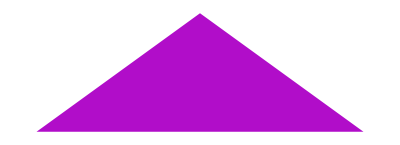
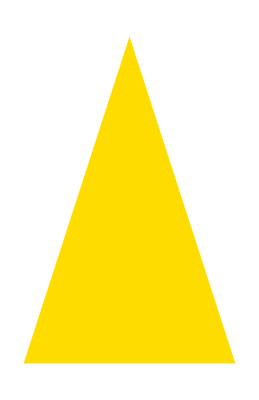

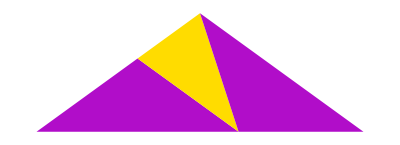
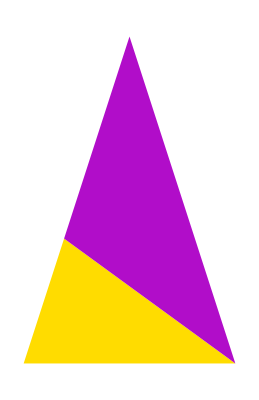

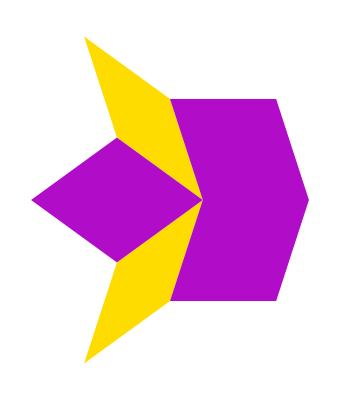
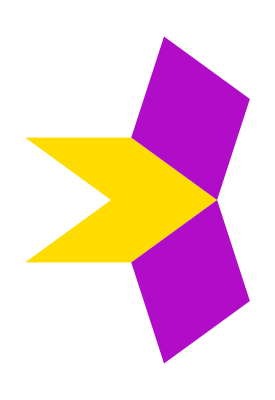

```mathematica
See/@{{unitfat},{unitskinny}}
See@Inflate[#,1]&/@{{unitfat},{unitskinny}}
See@FullInflate[#,1]&/@{{unitfat},{unitskinny}}
```

## Generate Large Tilings from Substitution Rules:

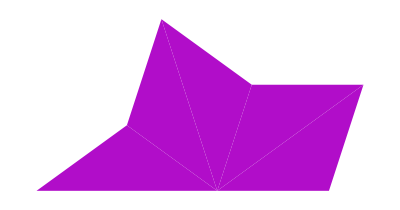

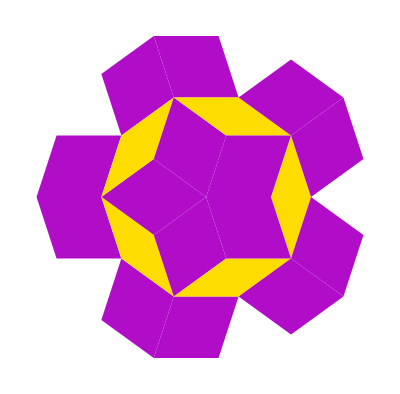
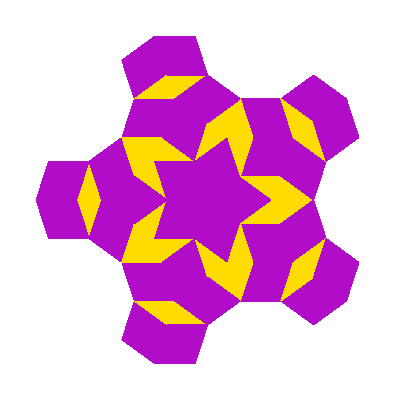
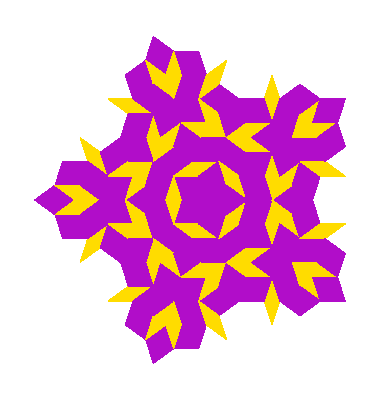
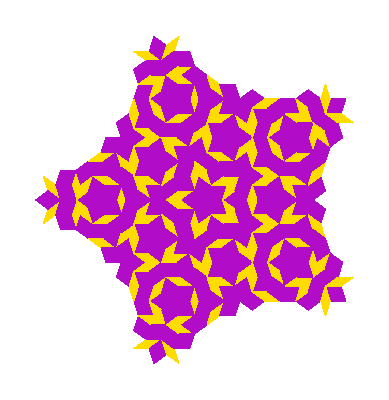
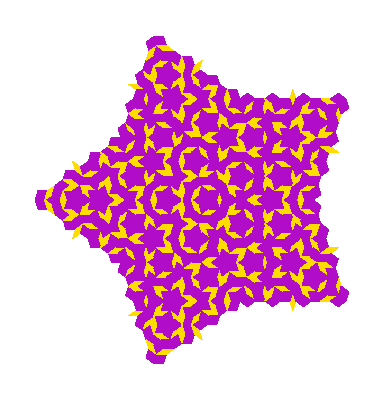
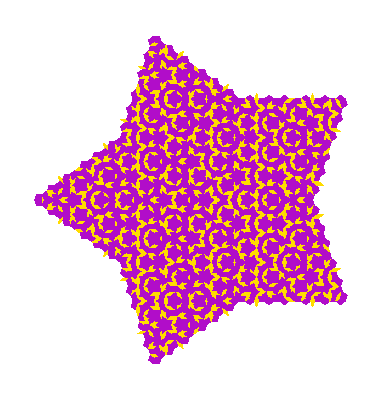
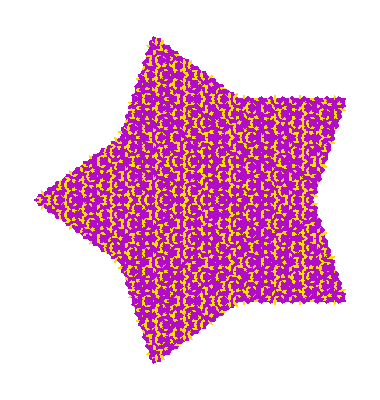

```mathematica
See@starseed
Table[See@FullInflate[starseed,i],{i,1,7}]
Show[See@FullInflate[starseed,9],ImageSize->Large]
```

## Slide Tiling to Illustrate Translational Symmetry

```mathematica
graphic={FaceForm[None],Polygon/@Coor/@Δ/@#1}&@FullInflate[starseed,9];
x=0.527; 
(*x=1.91;*)
y=0;
```

```mathematica
{Slider[Dynamic[x],{0,2}],Dynamic@x}
{Slider[Dynamic[y]],Dynamic@y}
Show[{Graphics[{EdgeForm[{NiceRed}],graphic},PlotRange->{{-2,2},{-2,2}}],Graphics[Translate[{Opacity[1],EdgeForm[Gray],graphic},Dynamic[{x,y}]]]},ImageSize->Large]
```

{,}

{,}

-Graphics-

## Rotate Tiling to Illustrate Fivefold Rotational Symmetry

```mathematica
θ=0;
{Slider[Dynamic[θ],{0,2Pi/5}],Dynamic@θ}
Show[{Graphics[{EdgeForm[{NiceRed}],graphic},PlotRange->{{-2,2},{-2,2}}],Graphics[Rotate[{Opacity[1],EdgeForm[Gray],graphic},Dynamic[θ],{0,0}]]},ImageSize->Large]
```

{,}

-Graphics-

## Collins’ Paths on Tiling

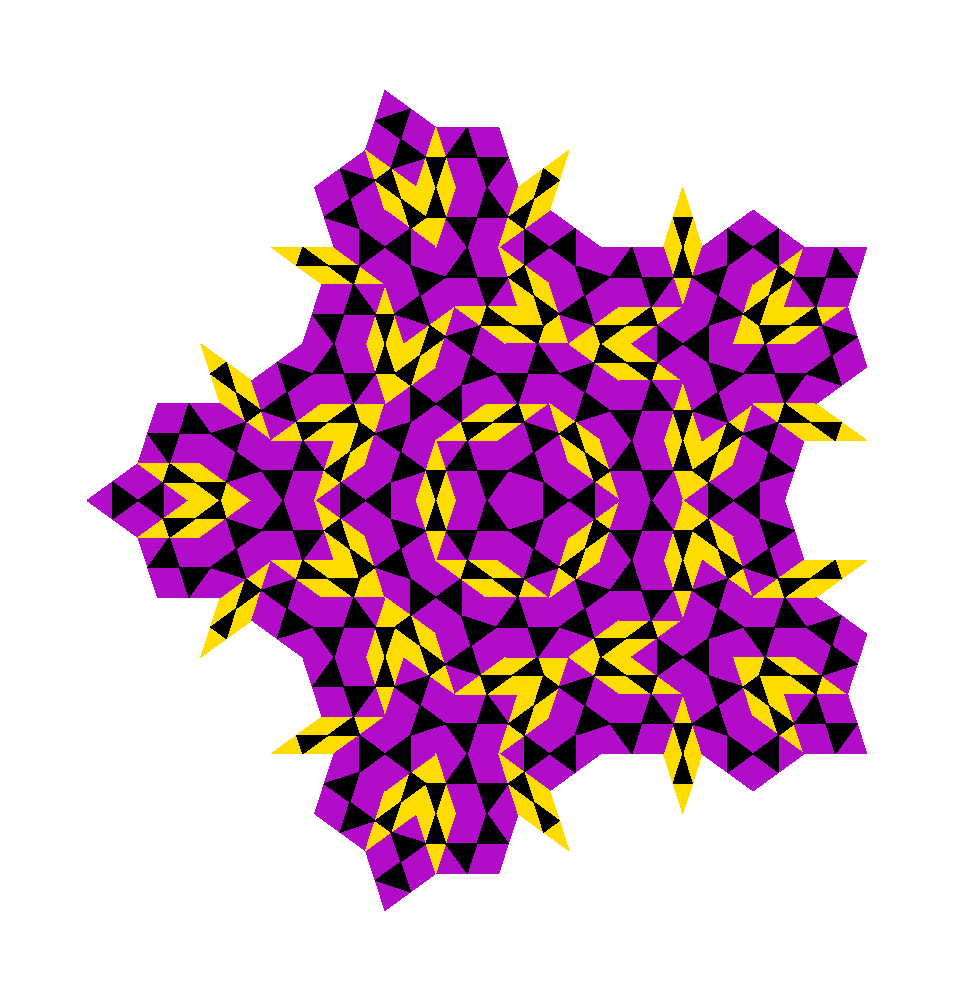

```mathematica
tiling=FullInflate[starseed,3];
pathtris=Midpoints/@MakePathTriangles@tiling;
Show[See@(tiling),SeeTri/@pathtris]
```

-Graphics-

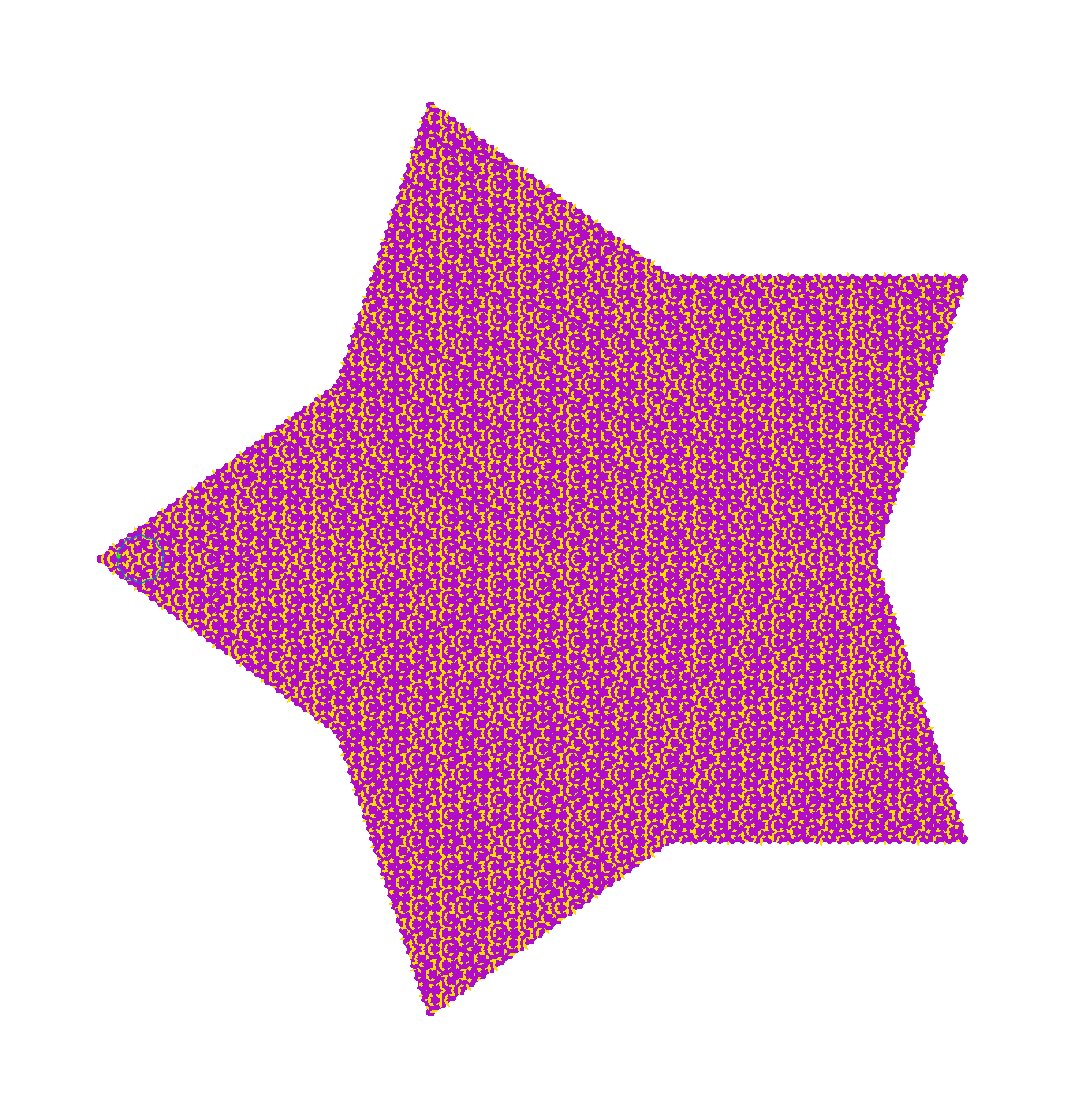

$Aborted

```mathematica
Show[See@tiling,SeeTri/@pathtris,Graphics[{NiceBlue,Thick,#}]&/@GeneratePath[{pathtris,56,3,1}],Graphics[{Thick,Green,Point[Coor@{pathtris[[56,3]]}]}]]
Show[See@tiling,Graphics[{NiceBlue,Thick,#}]&/@GeneratePath[{pathtris,56,3,1}],Graphics[{Thick,Green,Point[Coor@{pathtris[[56,3]]}]}]]
Show[SeeEdges@tiling,Graphics[{NiceRed,Thick,#}]&/@GeneratePath[{pathtris,56,3,1}],Graphics[{Thick,Green,Point[Coor@{pathtris[[56,3]]}]}]]
```

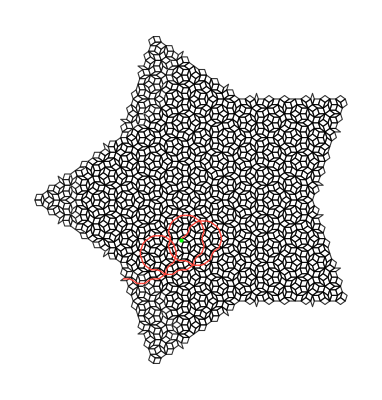

```mathematica
tiling=FullInflate[starseed,6];
pathtris=Midpoints/@MakePathTriangles@tiling;
Show[SeeEdges@tiling,Graphics[{NiceRed,Thick,#}]&/@GeneratePath[{pathtris,1587,3,-1}],Graphics[{Thick,Green,Point[Coor@{pathtris[[1587,3]]}]}]]
```

```mathematica
tiling=FullInflate[starseed,9];
pathtris=Midpoints/@MakePathTriangles@tiling;
```

```mathematica
Show[SeeEdges@tiling,Graphics[{NiceRed,Thick,#}]&/@GeneratePath[{pathtris,14001,1,1}],Graphics[{Thick,Green,Point[Coor@{pathtris[[14001,1]]}]}]]
```

-Graphics-

## See Kites and Darts Tiling

```mathematica
Show[Graphics[{Thick,NiceRed,Kites[#]}],SeeEdges@{#}]&/@{unitfat,unitskinny}
```

{-Graphics-,-Graphics-}

```mathematica
Show[SeeEdges@FullInflate[starseed,3],Graphics[{NiceRed,Thick,Kites/@AddConj@Inflate[starseed,3]}]]
```

-Graphics-

```mathematica
Graphics[{Red,Kites/@AddConj@Inflate[starseed,8]}]
```

-Graphics-